# Trave appoggio-appoggio con carico distribuito uniforme

```mathematica
ClearAll["Global`*"]
v[s_] = c1+c2*s+c3*Cos[α*s] + c4*Sin[α*s] + q0/(2*α^2*B)*s^2
```

c1+c2 s+(q0 s^2)/(2 B α^2)+c3 Cos[s α]+c4 Sin[s α]

```mathematica
{RR, MM}= CoefficientArrays[
{
v[0] == 0, 
v''[0]==0,
v[l]==0,
v''[l]==0
}, {c1, c2, c3, c4}
]//Normal;
MatrixForm[MM]
MatrixForm[-RR]
```

(1 | 0 | 1 | 0
0 | 0 | -α^2 | 0
1 | l | Cos[l α] | Sin[l α]
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α])

(0
-q0/(B α^2)
-(l^2 q0)/(2 B α^2)
-q0/(B α^2))

```mathematica
detMM = Det[MM]
```

-l α^4 Sin[l α]

```mathematica
αcr = k*Pi/l;
MMcr = Simplify[MM/.α->αcr, Assumptions->k ∈ Integers]
```

{{1,0,1,0},{0,0,-(k^2 π^2)/l^2,0},{1,l,(-1)^k,0},{0,0,((-1)^(1+k) k^2 π^2)/l^2,0}}

```mathematica
{c1, c2, c3, c4} = LinearSolve[MM, -RR]
```

{-q0/(B α^4),-(l q0)/(2 B α^2),q0/(B α^4),(-q0 Cot[l α]+q0 Csc[l α])/(B α^4)}

```mathematica
B=.;
l=.;
q0=.;
α=.;
k = .;

v[s]//FullSimplify
v[l/2]//Simplify
```

(q0 (-2+s (-l+s) α^2+2 Cos[s α]+2 Sin[s α] Tan[(l α)/2]))/(2 B α^4)

-(q0 (8+l^2 α^2-8 Sec[(l α)/2]))/(8 B α^4)

```mathematica
v'[s]//FullSimplify
```

-(q0 ((l-2 s) α+2 Sin[s α]-2 Cos[s α] Tan[(l α)/2]))/(2 B α^3)

-0.015647-0.0625439 s+0.0625439 s^2+0.015647 Cos[2.82743 s]+0.0987911 Sin[2.82743 s]

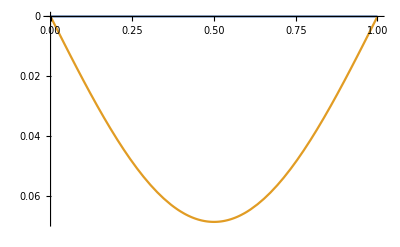

```mathematica
B=1;
l=1;
q0=1;
α=k*Pi/l;
k = .9;

v[s]
Show[
Plot[{0,v[s]}, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[{0,v'[s]}, {s, 0, l}, ScalingFunctions->"Reverse"]
]
```

```mathematica
B=.;
l=.;
q0=.;
α=.;
k =.;

δ = v[l/2]//Simplify
δ0 = Limit[v[l/2], α->0]

θA = v'[0]
θ0A = Limit[v'[0], α->0]
```

-(q0 (8+l^2 α^2-8 Sec[(l α)/2]))/(8 B α^4)

(5 l^4 q0)/(384 B)

-(l q0)/(2 B α^2)+(-q0 Cot[l α]+q0 Csc[l α])/(B α^3)

(l^3 q0)/(24 B)

```mathematica
fstabδ[α_] =δ/δ0//Simplify
fstabθ[α_] = θA/θ0A//Simplify
```

-(48 (8+l^2 α^2-8 Sec[(l α)/2]))/(5 l^4 α^4)

-(12 (l α+2 Cot[l α]-2 Csc[l α]))/(l^3 α^3)

```mathematica
Limit[fstabδ[α], α->0]
Limit[fstabδ[α], α->Pi/l]

Limit[fstabθ[α], α->0]
Limit[fstabθ[α], α->Pi/l]
```

1

Indeterminate

1

Indeterminate

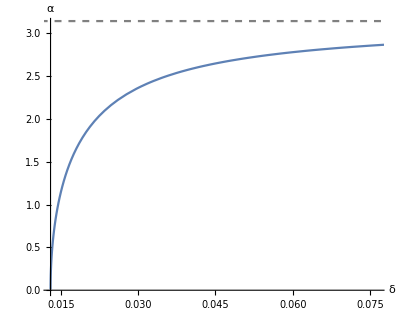

```mathematica
l=1;
B=1;
q0=1;
Show[
ParametricPlot[{δ,α}, {α, 0.01, .99Pi},AspectRatio->GoldenRatio/2, AxesLabel->{"δ", "α"}, PlotRange->{Automatic, Automatic}],
Plot[Pi, {δ, 0, 1}, PlotStyle->{{Gray, Dashed}}]
]
```

# Trave appoggio-appoggio con momento W in s=l

```mathematica
ClearAll["Global`*"]

v[s_]= v[s_] = c1+c2*s+c3*Cos[α*s] + c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0]==0, 
v''[0]==0, 
v[l]==0, 
-B*v''[l]==W
}, 
{c1, c2, c3, c4}
]//Normal;
MatrixForm[MM]
RR = -RR;
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 0 | -α^2 | 0
1 | l | Cos[l α] | Sin[l α]
0 | 0 | B α^2 Cos[l α] | B α^2 Sin[l α])

(0
0
0
W)

```mathematica
{c1,c2, c3, c4}=LinearSolve[MM, RR]
v[s]//Simplify
v'[s] //Simplify
```

{0,-W/(B l α^2),0,(W Csc[l α])/(B α^2)}

(W (-s+l Csc[l α] Sin[s α]))/(B l α^2)

(W (-1+l α Cos[s α] Csc[l α]))/(B l α^2)

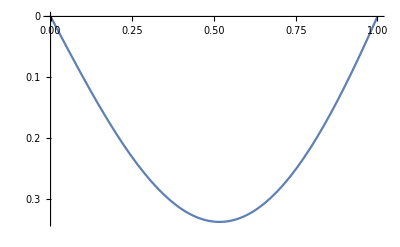

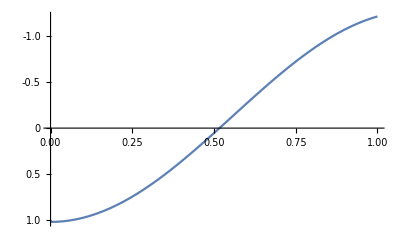

```mathematica
B=1;
l=1;
α=.9 Pi/l;
W=1;
Plot[v[s], {s, 0, 1}, ScalingFunctions->"Reverse"] 
Plot[v'[s], {s, 0, 1}, ScalingFunctions->"Reverse"]
```

```mathematica
ClearAll[W, B, α, θA,θB, l]

θA = v'[0]//Simplify
```

(W (-1+l α Csc[l α]))/(B l α^2)

```mathematica
θB = v'[l]//Simplify
```

(W (-1+l α Cot[l α]))/(B l α^2)

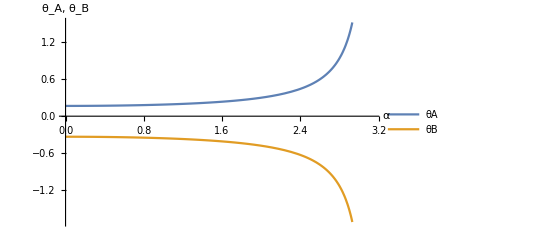

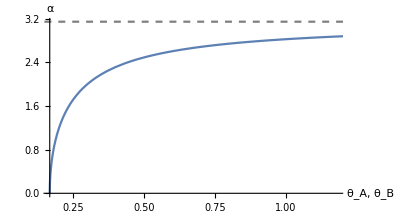

```mathematica
B=1;
l=1;
W=1;
Plot[{θA, θB}, {α, .001, .999Pi}, PlotLegends->"Expressions",AxesLabel->{"α","θ_A, θ_B"}]

Show[
ParametricPlot[{θA, α}, {α, .001, .999Pi}, AspectRatio->GoldenRatio/3, AxesLabel->{"θ_A, θ_B","α"}],
ParametricPlot[{θB, α}, {α, .001, .999Pi}, AspectRatio->GoldenRatio/3],
Plot[Pi, {α, .001, .999Pi}, PlotStyle->{{Gray, Dashed}}]
]
```

```mathematica
ClearAll[W, B, α, l, fstab, fstabδ, fstabθ]

θA0 = W*l/(6B);
θB0 = W*l/(3B);

fstabA = θA/θA0//FullSimplify
```

(6 (-1+l α Csc[l α]))/(l^2 α^2)

```mathematica
fstabB = θB/θB0//FullSimplify
```

(3 (-1+l α Cot[l α]))/(l^2 α^2)

```mathematica
Limit[fstabA,α->0]
Limit[fstabB,α->0]

Limit[fstabA,α->Pi/l]
Limit[fstabB,α->Pi/l]
```

1

-1

Indeterminate

Indeterminate

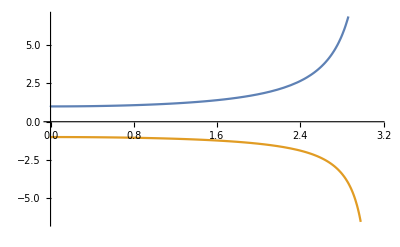

```mathematica
B=1;
l=1;
W=1;
Plot[{fstabA, fstabB}, {α, 0, Pi}]
```

# Trave a mensola con carico distribuito uniforme (?)

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s] + c4*Sin[α*s] + q0/(2*α^2*B)*s^2;

{RR, MM} = CoefficientArrays[
{
v[0]==0, 
v'[0]==0, 
v''[l]==0, 
-(v'''[l]+α^2*v'[l])==0
},
{c1, c2, c3, c4}
]//Normal;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
0 | -α^2 | 0 | 0)

(0
0
q0/(B α^2)
-(l q0)/B)

```mathematica
{c1, c2, c3, c4}=LinearSolve[MM, RR]
```

{-(q0 (-Sec[l α]+l α Tan[l α]))/(B α^4),(l q0)/(B α^2),(q0 (-Sec[l α]+l α Tan[l α]))/(B α^4),-(l q0)/(B α^3)}

```mathematica
v[s]//FullSimplify
```

(q0 s (2 l+s) α^2-2 q0 Sec[l α] (-1+Cos[s α]+l α (Sin[l α]-Sin[(l-s) α])))/(2 B α^4)

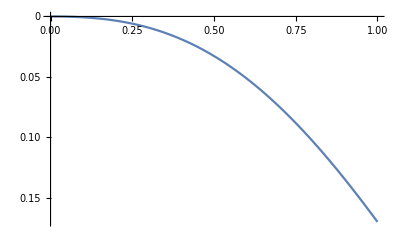

```mathematica
B=1;
l=1;
q0=1;
α=.9*Pi/l;
Plot[v[s], {s, 0, l}, ScalingFunctions->"Reverse"]
```

```mathematica
ClearAll[B, l, q0, fstab, fstabδ, δ0, δ, α]

δ0 = q0*l^4/(8B);
δ = v[l]//FullSimplify

fstabδ = δ/δ0
```

(q0 (-2+3 l^2 α^2+2 Sec[l α]-2 l α Tan[l α]))/(2 B α^4)

(4 (-2+3 l^2 α^2+2 Sec[l α]-2 l α Tan[l α]))/(l^4 α^4)

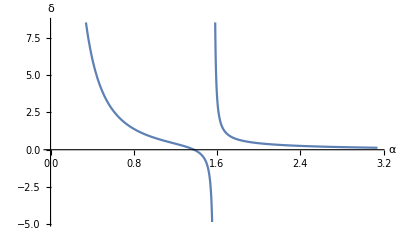

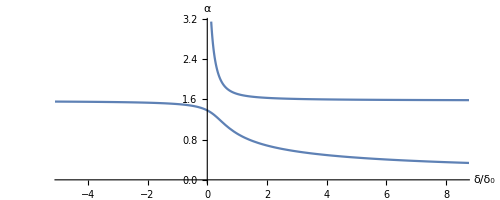

```mathematica
B=1;
l=1;
q0=1;

Plot[{δ}, {α, 0, Pi}, AxesLabel->{"α", "δ"}]
ParametricPlot[{δ, α}, {α, 0, Pi}, AxesLabel->{"δ/δ_0","α"}]
```

```mathematica
ClearAll[B, l, q0]

Limit[(q0 (-2+3 l^2 α^2+2 Sec[l α]-2 l α Tan[l α]))/(2 B α^4), α->0]
```

(q0 DirectedInfinity[Sign[l]^2])/B

# Trave a mensola con momento W in s=l

```mathematica
ClearAll["Global`*"]

v[s_]= v[s_] = c1+c2*s+c3*Cos[α*s] + c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0]==0, 
v'[0]==0, 
v''[l]==-W/B, 
-(v'''[l]+α^2 v'[l])==0
}, 
{c1, c2, c3, c4}
]//Normal;
MatrixForm[MM]
RR = -RR;
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
0 | -α^2 | 0 | 0)

(0
0
-W/B
0)

```mathematica
{c1,c2, c3, c4}=LinearSolve[MM, RR]
v[s]//Simplify
v'[s] //Simplify
```

{-(W Sec[l α])/(B α^2),0,(W Sec[l α])/(B α^2),0}

(W (-1+Cos[s α]) Sec[l α])/(B α^2)

-(W Sec[l α] Sin[s α])/(B α)

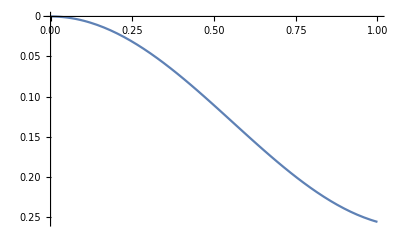

```mathematica
B=1;
l=1;
α=.9 Pi/l;
W=1;
Plot[v[s], {s, 0, 1}, ScalingFunctions->"Reverse"]
```

```mathematica
ClearAll[W, B, α, θA,θB, l]

θB = v'[l]//Simplify
θB0 = Limit[v'[l], α->0]
```

-(W Tan[l α])/(B α)

-(l W)/B

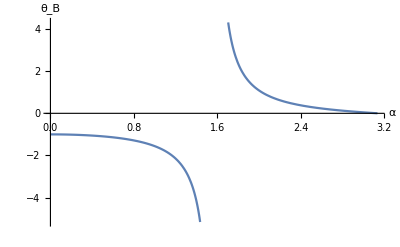

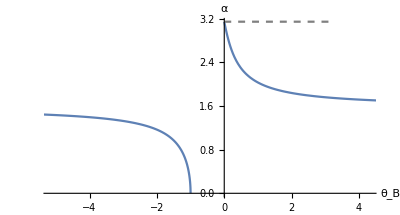

```mathematica
B=1;
l=1;
W=1;
Plot[{θB}, {α, .001, .999Pi}, PlotLegends->"Expressions",AxesLabel->{"α","θ_B"}]

Show[
ParametricPlot[{θB, α}, {α, .001, .999Pi}, AspectRatio->GoldenRatio/3, AxesLabel->{"θ_B","α"}],
Plot[Pi, {α, .001, .999Pi}, PlotStyle->{{Gray, Dashed}}]
]
```

```mathematica
ClearAll[W, B, α, l, fstab, fstabδ, fstabθ]

fstabB = θB/θB0//FullSimplify
```

Tan[l α]/(l α)

```mathematica
Limit[fstabB,α->0]
Limit[fstabB,α->3/2 Pi/l]
```

1

Indeterminate

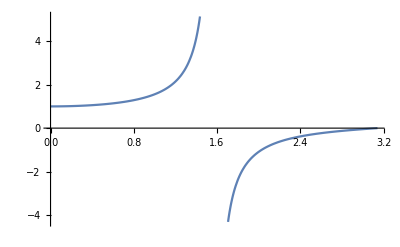

```mathematica
B=1;
l=1;
W=1;
Plot[{fstabB}, {α, 0, Pi}]
```